Note: requires CRNSimulatorSSA.m to be loaded.

Note that the input format to SimulateRxnsysSSA is consistent with SimulateRxnsys in that a reaction system is created with rxn and conc statements. Arbitrary order (zero-order, unimolecular, bimolecular, etc) reactions are supported. The output of SimulateRxnsysSSA is a TimeSeries object (list of discrete times and corresponding molecular counts).

See documentation for SimulateRxnsysSSA:

```mathematica
?SimulateRxnsysSSA
```

SimulateRxnsysSSA[rxnsys,endtime] runs Gillespie's SSA simulation of the reaction system rxnsys for time 0 to endtime or until no further reactions are possible. Set endtime to ∞ to continue until no further reactions are possible. In rxnsys, reactions are specified by rxn statements (arbitrary order reactions are allowed: eg rxn[a+a+b,c+c,1], including zero-order reactions), and initial molecular counts are specified by conc statements. If no initial count is set for a species, its initial count is set to 0. SimulateRxnsysSSA returns a TimeSeries object of reaction firing times and the corresponding molecular counts. The propensity of reaction a→… is k*a, the propensity of reaction a+b→… is k*a*b, and the propensity of reaction a+a→… is k*a*(a-1), etc.

### Approximate majority

```mathematica
n=1000;
```

```mathematica
rsys={
rxn[x+y,x+b,1/n],
rxn[x+y,y+b,1/n],
rxn[x+b,2x,1/n],
rxn[y+b,2y,1/n],

conc[{x,y},n/2]};
```

```mathematica
(* Simulate until no further reactions are possible *)
trajectory=SimulateRxnsysSSA[rsys,∞];
```

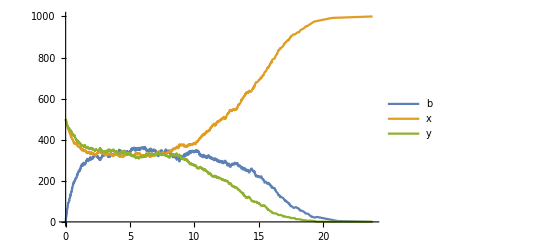

```mathematica
ListLinePlot[
trajectory,
PlotRange->{0,All},
PlotLegends->SpeciesInRxnsys[rsys],
MaxPlotPoints->500 (* Limit the number of points to plot faster *)]
```

### Predator-prey

```mathematica
n=300;
```

```mathematica
tmax=50;
```

```mathematica
rsys={
rxn[x1+x2,2x2,1/n],
rxn[x1,2x1,1],
rxn[x2,1,1],

conc[{x1,x2},n/2]};
```

```mathematica
(* Simulate for tmax time *)
trajectory=SimulateRxnsysSSA[rsys,tmax];
```

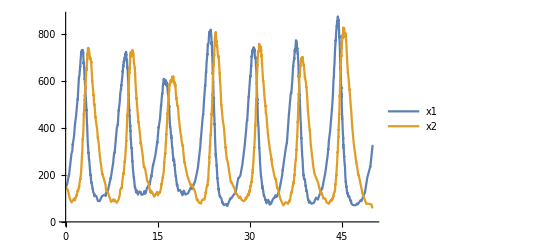

```mathematica
ListLinePlot[
trajectory,
PlotRange->{0,All},
PlotLegends->SpeciesInRxnsys[rsys],
MaxPlotPoints->500 (* Limit the number of points to plot faster *)]
```

The TimeSeries object “trajectory” can be used as either a list of times and counts, or counts as a function of t (a continuous variable). Thus we can also pass it to Plot as follows.

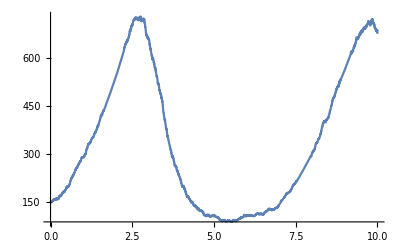

```mathematica
(* trajectory[t] represents the counts of species as a function of t *)
Plot[trajectory[t]⟦1⟧, {t,0,10}, PlotRange->All]
```